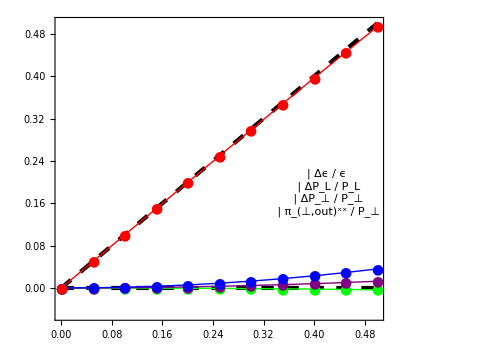

```mathematica
(*ANISOTROPIC HADRON RESONANCE GAS*)

T0 = 0.155;
αT = 1.118756;
αL = 0.7520408;
Λ = 0.1562006; (* GeV *)
frac=Table[0.05*i,{i,0,10}];

(*I should plot the PL and PT matching conditions*)
(*As well as the pi_perp_xx*)

Δϵoverϵdata = {0.0,0.0001272,0.0005089,0.001145,0.002036,0.003182,0.004583,0.006239,0.008151,0.01032,0.01275};

ΔPLoverPLdata = {0.0,-3.314*10^-5,-0.0001327,-0.0002991,-0.0005332,-0.000836,-0.001209,-0.001654,-0.002172,-0.002767,-0.003441};

ΔPToverPTdata ={0.0,0.000358,0.001432,0.003223,0.005732,0.008961,0.01291,0.01758,0.02298,0.02911,0.03598};

piperpoverPTdata = {0.0,0.04999,0.09995,0.1498,0.1996,0.2492,0.2986,0.3478,0.3967,0.4453,0.4935};

style={Directive[RGBColor[0,0,0],AbsoluteThickness[3],Dashing[Medium]],Directive[RGBColor[0,0,0],AbsoluteThickness[3],Dashing[Medium]]};

legend1=Panel[Grid[{{Graphics[{Purple,Disk[]},ImageSize->10],Style["Δϵ / ϵ",FontSize->16]},

{Graphics[{Green,Disk[]},ImageSize->10],Style["ΔP_L / P_L",FontSize->16]},{Graphics[{Blue,Disk[]},ImageSize->10],Style["ΔP_⊥ / P_⊥",FontSize->16]},
{Graphics[{Red,Disk[]},ImageSize->10],Style["π_(⊥,out)^xx / P_⊥",FontSize->16]}}],Background->White];

Δϵoverϵplot = Table[{frac[[i]],Δϵoverϵdata[[i]]},{i,1,Length[frac]}];
ΔPToverPTplot = Table[{frac[[i]],ΔPToverPTdata[[i]]},{i,1,Length[frac]}];
ΔPLoverPLplot  = Table[{frac[[i]],ΔPLoverPLdata [[i]]},{i,1,Length[frac]}];
piperpoverPTplot = Table[{frac[[i]],piperpoverPTdata[[i]]},{i,1,Length[frac]}];

Show[{{
Plot[{x,0.0},{x,0,0.5},PlotRange->{-0.-0.05,0.5},ImageSize->{500,400},PlotStyle->style,Frame->True,Axes->False,BaseStyle->{FontSize->18},AspectRatio->0.7],
ListPlot[{ΔPLoverPLplot,Δϵoverϵplot,ΔPToverPTplot,piperpoverPTplot},Joined->{True},PlotRange->{-0.1,0.5},ImageSize->600,Frame->True,Axes->False,PlotMarkers->{{●,14},{●,14},{●,14},{●,14}},PlotStyle->{{Green,Thick},{Purple,Thick},{Blue,Thick},{Red,Thick}},BaseStyle->{FontSize->18},AspectRatio->0.7]}
},Epilog->{Inset[legend1,{0.42,0.18}]},ImageSize->{500,400},FrameLabel->{"π_(⊥,in)^xx / P_⊥"}]
```